The number of pixels and the FOV are limited by the laser repetition rate, i.e., how many laser pulses can fit in a scanned line.
For a 80 MHz laser and 8 kHz scanner, there are 80 MHz/(2*8 kHz) = 5000 pulses. If roughly speaking we have 10 pulses per pixel, then there could be max 500 pixels

```mathematica
μm = 10^-6;
μs=10^-6;
ms=10^-3;
ns = 10^-9;
mm=10^-3;
kHz=10^3;
Tline=62.5μs;(*Time per scanned line*)
Tlaser = 12.5ns;(*Laser pulse repetition period*)
tFPGA = 6.25ns;(*Clock of the FPGA*)
Δx=0.5μm;(*Sampling resolution*)
γ=0.8;(*filling factor that removes the dead time at the turning points*)
L=250μm; (*Full scan in μm*)
FOV=γ L;(*Effective field of view of the microscope*)
NpixFull=500;(*Full pixel number*)
NpixPartial= γ NpixFull;(*Effective pixel number*)
```

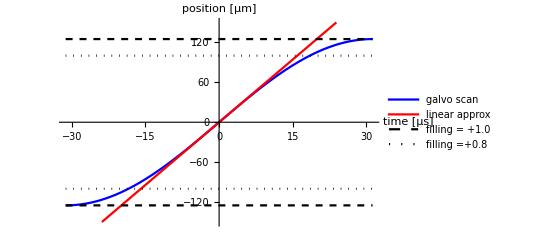

```mathematica
RSposition[t_]:=L/2 Sin[π/Tline t](*Position of the resonant scanner vs time*)
Plot[{RSposition[t μs]/μm,(L π)/(2Tline)t μs/μm,{L/2,-L/2}/μm,γ{L/2,-L/2}/μm },{t,-Tline/2/μs,Tline/2/μs},PlotRange->{-150,150},PlotStyle->{Blue,Red,{Dashed,Black},{Dotted,Black}},AxesLabel->{"time [μs]","position [μm]"} , PlotLegends->{"galvo scan","linear approx","filling = +1.0","filling =" +γ}]
```

```mathematica
DiscretePosition[pix_]:=Δx*pix(*Spatial discretization*)
```

```mathematica
time[x_]:=Tline/π ArcSin[2/L x](*Convert from spatial coordinate to time*)
DiscreteTime[pix_]:=Re[time[DiscretePosition[pix]]](*Time discretization mapped from the spatial discretization. It should equal to L/2*)

AmplitudeFull= DiscretePosition[NpixFull/2];(*Amplitude of a full linescan. The FFOV is 2X this amount*)
tLinescanFull=2*DiscreteTime[NpixFull/2];(*Time to perform a full linescan (in half of the period, Tline/2)*)
AmplitudePartial= DiscretePosition[NpixPartial/2];(*Amplitude of a partial linescan. The FFOV is 2X this amount*)
tLinescanPartial=2*DiscreteTime[NpixPartial/2];(*Time to perform a partial linescan*)

(*Tabulate the position vs time*)
header={"pixel","Position [μm]","Time [μs]"};
TableForm[Prepend[Table[{pix,DiscretePosition[pix]/μm,DiscreteTime[pix]/μs},{pix,NpixFull/2,0,-1}],header]];
```

```mathematica
tdwell[pix_]:=DiscreteTime[pix]-DiscreteTime[pix-1](*Dwell time*)
PulsesPerPixel[pix_]:=tdwell[pix]/Tlaser (*Number of laser pulses that fit in the dwell time*)
PulsesPerPixelNorm[pix_]:=tdwell[0]/tdwell[pix](*Longer dwell times have a higher pulse counts. The pulse-count must be normalized*)

tLineScanFull = Sum[tdwell[i]/μs,{i,-NpixFull/2+1,NpixFull/2}];(*The sum of all the dwell times should equal a full scan. Compare*)
tLineScanPartial  = Sum[tdwell[i]/μs,{i,-NpixPartial/2+1,NpixPartial/2}];(*The sum of all the dwell times should equal the partial scan*)

(*Tabulate the dwell time*)
header={"pixel i","pixel i-1","Dwell [ns]","Pulses per pix", "Normalization factor"};
TableForm[Prepend[Table[{pix,pix-1,tdwell[pix]/ns,PulsesPerPixel[pix],PulsesPerPixelNorm[pix]},{pix,NpixPartial/2,1,-1}],header]];
```

Now the practical case which considers the discrete nature of the FPGA clock

```mathematica
tdwellPract[pix_]:=tFPGA Round[tdwell[pix]/tFPGA]
PulsesPerPixelPract[pix_]:=tdwellPract[pix]/Tlaser
PulsesPerPixelNormPract[pix_]:=tdwellPract[NpixPartial/2]/tdwellPract[pix]
```

```mathematica
(*Tabulate the dwell time*)
header={"pixel i","pixel i-1","Pract dwell [ns]","Pract pulses per pix", "Pract normalization factor"};
TableForm[Prepend[Table[{pix,pix-1,tdwellPract[pix]/ns,PulsesPerPixelPract[pix],PulsesPerPixelNormPract[pix]},{pix,NpixPartial/2,1,-1}],header]];
```

```mathematica
tLineScanPartialPract=Sum[tdwellPract[i],{i,-NpixPartial/2+1,NpixPartial/2}];(*Time to perform a partial linescan*)
AmplitudePartialPract= RSposition[tLineScanPartialPract/2];(*Amplitude of a partial linescan. The FFOV is 2X this amount*)
γPract=AmplitudePartialPract/(L/2);(*Practical filling factor*)
```

```mathematica
(*Summary*)
Grid[{{"","Full-scan amplitude[μm]","full linescan time[μs]","Partial-scan amplitude[μm]","partial linescan time[μs]","γ"},
{"Exact",AmplitudeFull/μm,tLinescanFull/μs,AmplitudePartial/μm,tLinescanPartial/μs,γ},
{"Practical","","",AmplitudePartialPract/μm,tLineScanPartialPract/μs, γPract}},Frame->All]
```

| Full-scan amplitude[μm] | full linescan time[μs] | Partial-scan amplitude[μm] | partial linescan time[μs] | γ
Exact | 125. | 62.5 | 100. | 36.8959 | 0.8
Practical |  |  | 100.125 | 36.9625 | 0.801003

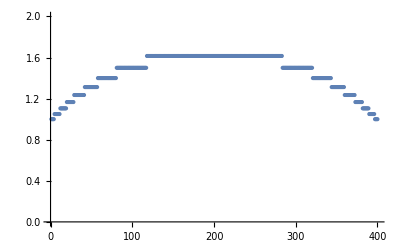

```mathematica
ListPlot[Table[PulsesPerPixelNormPract[pix],{pix,NpixPartial/2,-NpixPartial/2+1,-1}],PlotRange->{0,2}]
```

```mathematica
.
```